# network exp. free space MOT beam alignment

P. Huft

```mathematica
SetDirectory[NotebookDirectory[]];
```

## 2023.4.04

Images of the free space beam profiles in order to accurately know the beam waists and balance the intensities.

```mathematica
data5=ImageData[ColorConvert[Import["mot beam 5 6.24mm asphere 20230404.bmp"],"Grayscale"]];
data6=ImageData[ColorConvert[Import["mot beam 6 MOT tube 5mm planoconvex 20230404.bmp"],"Grayscale"]];
```

```mathematica
data5=(data5/Max[data5])[[280;;780,440;;940]];
data6=(data6/Max[data6])[[280;;780,440;;940]];
```

```mathematica
Max[data5]
```

1.

```mathematica
data5//Dimensions
```

{1080,1440}

```mathematica
Image[data5]
```

-Graphics-

```mathematica
Image[data6]
```

-Graphics-

```mathematica
data5[[577,711]]
```

0.94012

```mathematica
{imax,jmax}=data5//Dimensions;
data5Coordinated=Flatten[Table[{i,j,data5[[i,j]]},{i,Range[imax]},{j,Range[jmax]}],1];
```

```mathematica
model=a Exp[(-2(x-x0)^2)/wx^2]Exp[(-2(y-y0)^2)/wy^2];
```

```mathematica
fit5=FindFit[data5Coordinated,model,{{a,1},{x0,259},{y0,292},{wx,100},{wy,100}},{x,y}]
```

{a→0.811296,x0→275.23,y0→258.314,wx→151.777,wy→150.74}

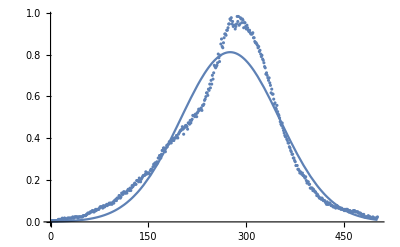

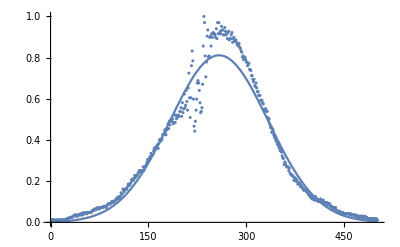

```mathematica
{xmax,ymax}=Dimensions[data5];
Show[Plot[(model/.fit5)/.y->258.303,{x,0,xmax}],ListPlot[data5[[;;,Floor[258.303+0.5]]]],PlotRange->All]
Show[Plot[(model/.fit5)/.x->275.256,{y,0,ymax}],ListPlot[data5[[Floor[275.256+0.5],;;]]],PlotRange->All]
```

```mathematica
(*{xmax,ymax}=Dimensions[data5]
ListPlot3D[GaussianFilter[data5Coordinated,10],PlotRange->{-0.1,1.1}],Plot3D[model/.fit,{x,0,xmax},{y,0,ymax}, PlotStyle->Directive[Opacity[0.8],Red],PlotRange->{-0.1,1.1}]]*)
```

```mathematica
{imax,jmax}=data6//Dimensions;
data6Coordinated=Flatten[Table[{i,j,data6[[i,j]]},{i,Range[imax]},{j,Range[jmax]}],1];
```

```mathematica
fit6=FindFit[data6Coordinated,model,{{a,1},{x0,300},{y0,295},{wx,100},{wy,100}},{x,y}]
```

{a→0.935545,x0→297.301,y0→291.28,wx→125.873,wy→105.384}

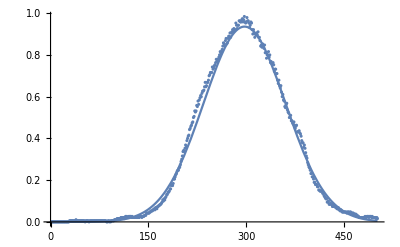

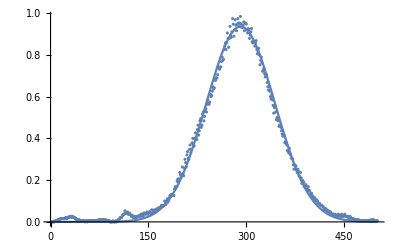

```mathematica
{xmax,ymax}=Dimensions[data5];
Show[Plot[(model/.fit6)/.y->291.375,{x,0,xmax}],ListPlot[data6[[;;,Floor[291.375+0.5]]]],PlotRange->All]
Show[Plot[(model/.fit6)/.x->297.375,{y,0,ymax}],ListPlot[data6[[Floor[297.375+0.5],;;]]],PlotRange->All]
```

```mathematica
{a5,x05,y05,wx5,wy5}=Values[fit5];
{a6,x06,y06,wx6,wy6}=Values[fit6];
(wx5 wy5)/(wx6 wy6)
```

1.72477

```mathematica
(*{xmax,ymax}=Dimensions[data6];
Show[ListPlot3D[dataCoordinated,PlotRange->{-0.1,1.1}],Plot3D[model/.fit,{x,0,xmax},{y,0,ymax}, PlotStyle->Directive[Opacity[0.7],Red]]]*)
```